## Import data

```mathematica
ClearAll["Global`*"]
```

```mathematica
parampath="/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-ba130/fit_params.dat";
band1path="/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-ba130/ba_130_B1_band.dat";
band2path="/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-ba130/ba_130_B2_band.dat";
```

```mathematica
params=Flatten[Import[parampath]];
dataBand1=Import[band1path];
dataBand2=Import[band2path];
```

```mathematica
spinsband1=Table[dataBand1[[i,1]],{i,1,Length[dataBand1]}];
spinsband2=Table[dataBand2[[i,1]],{i,1,Length[dataBand2]}];
band1exp=Table[dataBand1[[i,2]],{i,1,Length[dataBand1]}];
band2exp=Table[dataBand2[[i,2]],{i,1,Length[dataBand2]}];
band1th=Table[dataBand1[[i,3]],{i,1,Length[dataBand1]}];
band2th=Table[dataBand2[[i,3]],{i,1,Length[dataBand2]}];
```

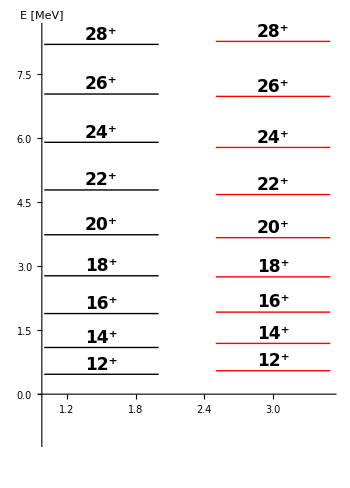

```mathematica
bandmaker[start_,shift_,energies_]:=Table[{{start,energies[[i]]},{start+shift,energies[[i]]}},{i,1,Length[energies]}];
energyplotter[energies_,color_]:=ListLinePlot[energies,Axes->{False,True,False,False},Frame->None,AxesStyle->Directive[Black,Thick],ImageSize->350,AspectRatio->1.4,PlotStyle->Directive[Thick,color],AxesLabel->{"","E [MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"}];
shower[energiesexp_,energiesth_]:=Show[energyplotter[bandmaker[1,1,energiesexp],1,Black],energyplotter[bandmaker[2.5,1,energiesth],2,Red],PlotRange->{Full,{Min[energiesexp]-1.5,Max[energiesexp]+0.3}},Epilog->{Table[Inset[Style[StringTemplate["(``)^+"][spinsband1[[i]]],Black,17,Bold,Italic],{1.5,energiesexp[[i]]+0.25}],{i,1,Length[energiesexp]}],Table[Inset[Style[StringTemplate["(``)^+"][spinsband1[[i]]],Black,17,Bold,Italic],{3,energiesth[[i]]+0.25}],{i,1,Length[energiesth]}]}];
shower[band1exp,band1th]
```